```mathematica
Subscript[h, 1][ν_, x_] := Sqrt[π]/2 HankelH1[ν, x]
```

```mathematica
Subscript[h, 2][ν_, x_] := Sqrt[π]/2 HankelH2[ν, x]
```

```mathematica
g[a_, ν_] := 204000/π^2 1/a NIntegrate[ξ Sin[ξ/102000 a]*Abs[Subscript[h, 1][ν, ξ a]*Subscript[h, 2][ν, ξ a]]*(Im[Subscript[h, 1][ν,ξ]*Subscript[h, 2][ν,ξ*a]])^2, {ξ, 0,∞}]
```

General::munfl: Exp[-1549.34] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.24851×10^-31 1.40175×10^-278 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 5.9334×10^-31 1.89939×10^-279 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

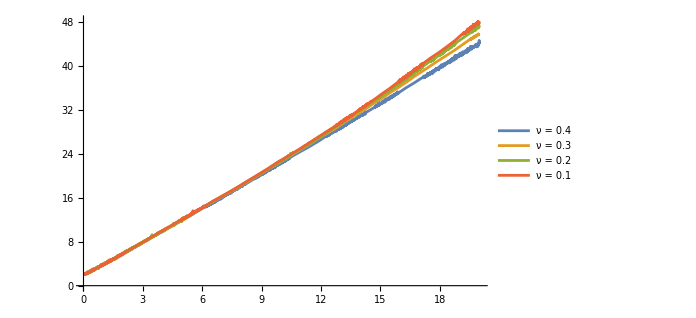

```mathematica
Plot[{-Log[g[Exp[t], 0.4]],-Log[g[Exp[t], 0.3]],-Log[g[Exp[t], 0.2]],-Log[g[Exp[t], 0.1]]}, {t, Log[1.05], 20},PlotLegends->{"ν = 0.4","ν = 0.3","ν = 0.2","ν = 0.1"}]
```

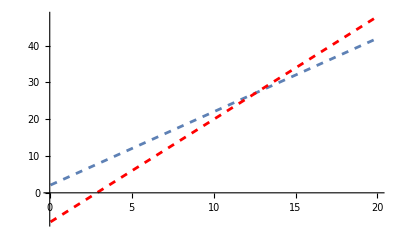

```mathematica
Plot[{2(t-3.89)+9.8, 2.8(t-19.98)+47.9}, {t,Log[1.05],20}, PlotStyle->{{Dashed},{Red,Dashed}}]
```

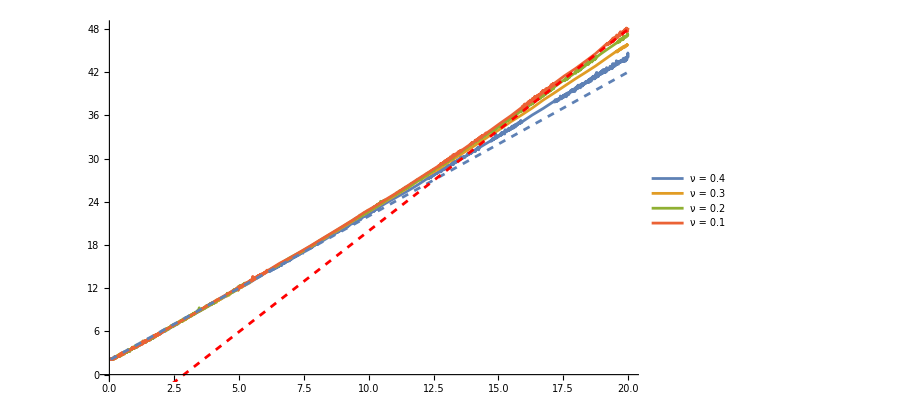

```mathematica
Show[Out[4],Out[7]]
```